## 6296549375 - Successfully concatinated

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
6296549375:{"AB"->"AA","A"->"B","B"->"AAAAA"}
```

```mathematica
rs01=FromReducedRankIndex[6296549375]
```

<|Index→6296549375,QCode→34232242423333,RuleSet→{AB→AA,A→B,B→AAAAA}|>

```mathematica
rs01[["RuleSet"]]
```

{AB→AA,A→B,B→AAAAA}



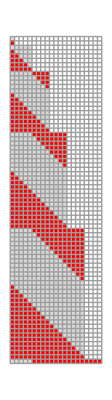
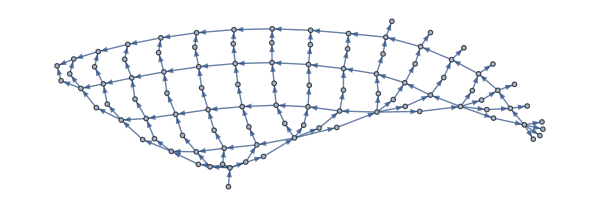
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "A",500,
 SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,2→3,2→4,2→5,2→6,2→7,3→8,«706»,451→495,452→496,453→497,454→498,455→499,456→500}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1},{1,2,3,4,5},{5},{5},{5},{5},{5},{1,5,6,7,8},{1,8},{1,8},{1,8},{8,9},{9},{9},{9},{9},{9},{9},{9},{9},{9},{1,9,10,11,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{13},{13},{13},{13},{13},{13},{13},{13},{13},{13},{13},{13},{13},{1,13,14,15,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{1,17,18,19,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{21},{1,21,22,23,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{25},{1,25,26,27,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{28,29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{29},{1,29,30,31,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{32,33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{1,33,34,35,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{36,37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{37},{1,37,38,39,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{40,41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{41},{1,41,42,43,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1},{1},{1},{1},{1}}

```mathematica
rslo1=ReduceSetList[nds01]
```

{{1},{1,2,3,4,5},€_(n$1⊨1)^9[€^(1+4 n$1)[{1+4 n$1}],{1,1+4 n$1,2 (1+2 n$1),3+4 n$1,4 (1+n$1)},€^(-1+4 n$1)[{1,4 (1+n$1)}],{4 (1+n$1),5+4 n$1}],€^41[{41}],{1,41,42,43,44},€^34[{1,44}],€^5[{1}]}